# Quantum Magnets + Impurity

This script employs exact diagonalization to compute the magnon spectrum and spin expectation values in  Quantum Magnets featuring a magnetic impurity.  We use the a spin Hamiltonian  in the Honeycomb lattice plus the magnetic Zeeman term for the bulk spin, and an antiferromagnetic (Heisenberg like) Kondo coupling of the impurity spin to the bulk. The impurity is couple to one site in the Adatom case and to three sites in the Substitutional case. We will consider
	•   spin 1/2 system with a impurity spin Simp= 1/2,1, or 3/2 [ e.g.  RuCl_3 with Simp=3/2 Cr^(3+)  impurity (e.g. 1704.03849 ) ]

In this Notebook we are preparing figures for the XXZ model :                                                                       
	•  Run  “XXZ.m”  to get the data for the according system size
	•  The function are defined in the package  “definition.wl”

```mathematica
Quit[]
```

## Preamble

```mathematica
Needs["MaTeX`"]

If[ ¬($FrontEnd===Null), SetDirectory[NotebookDirectory[]] ];

Get[ FileNameJoin[{Directory[],"definitions.wl" }] ];

figFolder =FileNameJoin[{NotebookDirectory[],"Figures" }];
createDirectory@figFolder;

opensMarker[coln_]:=Graphics[{coln[[1]],EdgeForm@Directive[coln[[1]],Thickness[.08]],Opacity[0.3],RegularPolygon[coln[[2]]]  }];
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

Figures-Kitaev

```mathematica
cyan=CMYKColor[.70,.20,0,0.2];
magenta=CMYKColor[0,.40,.31,0.1];
pink=CMYKColor[0,.91,.46,.08];
red=CMYKColor[0,.89,.88,.12];
blue=CMYKColor[1,.36,0,.40];
green=CMYKColor[.56,0,.58,.31];
```

## Figures - Adatom Case

Information/Parameters

eigenvalues and energy level are saved as
		. )  eValues and
		..)  eLevels
	with Context =  Ada/Sub, size LxLy, and  S spin imp
	e.g.  context=Ada33S15 for (Lx,Ly)=(3,3) and simp=3/2

### ADA S=1/2 Si=1/2 (Energy) (2x2)

h Range length= 201

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\Kitaev-S0.5_S0.5_ADA\XXZ_FM_ADA_size=(2,2)_Simp=0.5\h=Range[0,1,0.005]_JK={0.5}_k=20.txt

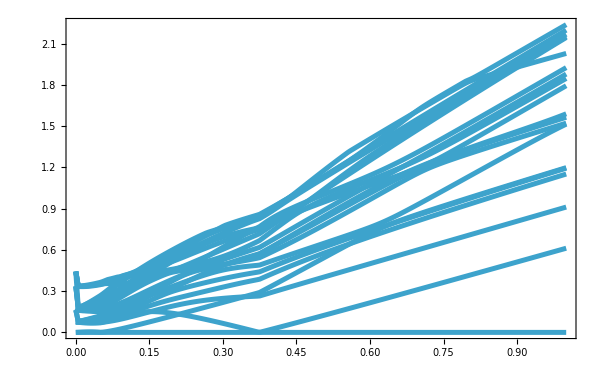

```mathematica
$FileName="Kitaev-S0.5_S0.5_ADA.m";

systemDimensions = {{2,2}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0 cvec}; 
bulkSpin         = {1/2};
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,1,.005};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 20; 
HamCoupling="XXZ_FM_ADA";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange; 

Print["h Range length= ",Length@hRange];


Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues,color1=cyan,color2=pink,
plotrange={{-.01,.78},{-.01,.78}}   },
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  Sort@dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;


(* Exporting to TXT*)
Module[{path0},
path0=FileNameJoin@{Directory[],"data","ED_Kitaev","Energy",StringJoin[scriptName, "_EN.txt"]};
dataWrite[path0,  Transpose[Thread/@levels]   ]; 
];
	plotTitle  = StringReplace[StringJoin[{"\\text{Adatom} \\quad  S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk "}],
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ JK  ],"g0"->ToString[Round@g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	

figDispED0=ListPlot[Transpose[Thread/@levels],PlotStyle->{{color1,Thickness[0.006] ,Opacity[1]}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)@"\\text{ED}" },LegendMarkers->Automatic],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> Full] 
]
```

### ADA S=1/2 Si=1/2 (Spin) (2x2)

h Range length= 201

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\Kitaev-S0.5_S0.5_ADA\XXZ_FM_ADA_size=(2,2)_Simp=0.5\h=Range[0,1,0.005]_JK={0.5}_spin_components.txt

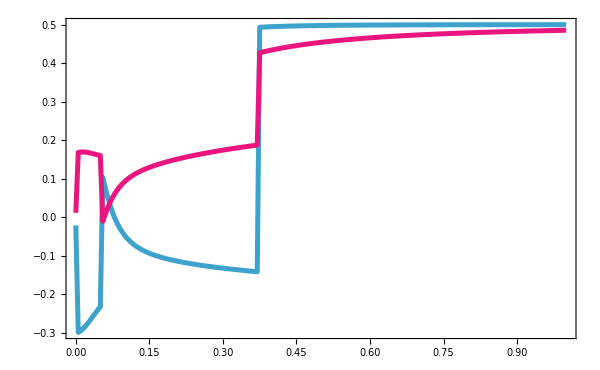

```mathematica
$FileName="Kitaev-S0.5_S0.5_ADA.m";

systemDimensions = {{2,2}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0 cvec}; 
bulkSpin         = {1/2};
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,1,.005};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 20; 
HamCoupling="XXZ_FM_ADA";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange; 

Print["h Range length= ",Length@hRange];


Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues,color1=cyan,color2=pink,
plotrange={{-.01,.78},{-.01,.78}}   },
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	
	{Lx,Ly}=Round@{Lx,Ly}; 
          scriptName= FileBaseName[$FileName]; 	
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataBulk=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];

(* Exporting to TXT*)
Module[{path1,path2},
path1=FileNameJoin@{Directory[],"data","ED_Kitaev","Spin",StringJoin[scriptName, "_Spin_Imp.txt"]};
path2=FileNameJoin@{Directory[],"data","ED_Kitaev","Spin",StringJoin[scriptName, "_Spin_Bulk.txt"]};
dataWrite[path1,dataSimp[[3]]  ]; 
dataWrite[path2,dataBulk[[3]]  ]; 
];

	plotTitle  = StringReplace[StringJoin[{"\\text{Adatom} \\quad  S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk "}],
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ JK  ],"g0"->ToString[Round@g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	

figSpinED=ListPlot[ {dataSimp[[3]], dataBulk[[3]]},PlotStyle->{{color1,Thickness[0.006] ,Opacity[1]},{color2,Thickness[0.006] ,Opacity[1]}},
Joined->True,
Frame->True,
FrameStyle->Directive[Black,18,Thickness[.002]],
PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)/@{"S_{\\text{imp} }","S_{1}"} },
LegendMarkers->Automatic],{Scaled[{.981,.9}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\left< \\mathbf{S}\\cdot\\hat{\\mathbf{c}} \\right> "},
ImageSize->600,
PlotRange-> Full] 
]
```

### ADA S=3/2 Si=1/2 (Energy) (2x2)

h Range length= 221

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\Kitaev-S1.5_S0.5_ADA\XXZ_FM_ADA_size=(2,2)_Simp=0.5\h=Range[0,2.2,0.01]_JK={0.5}_k=10.txt

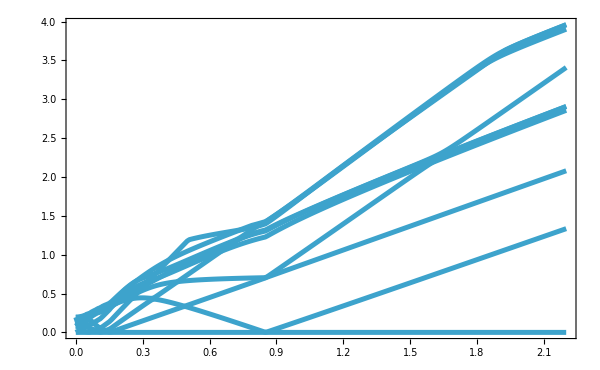

```mathematica
$FileName="Kitaev-S1.5_S0.5_ADA.m";

systemDimensions = {{2,2}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0 cvec}; 
bulkSpin         = {3/2};
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,2.2,.01};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 10; 
HamCoupling="XXZ_FM_ADA";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange; 

Print["h Range length= ",Length@hRange];


Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues,color1=cyan,color2=pink,
plotrange={{-.01,.78},{-.01,.78}}   },
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  Sort@dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;


(* Exporting to TXT*)
Module[{path0},
path0=FileNameJoin@{Directory[],"data","ED_Kitaev","Energy",StringJoin[scriptName, "_EN.txt"]};
dataWrite[path0,  Transpose[Thread/@levels]   ]; 
];
	plotTitle  = StringReplace[StringJoin[{"\\text{Adatom} \\quad  S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk "}],
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ JK  ],"g0"->ToString[Round@g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	

figDispED0=ListPlot[Transpose[Thread/@levels],PlotStyle->{{color1,Thickness[0.006] ,Opacity[1]}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)@"\\text{ED}" },LegendMarkers->Automatic],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> Full] 
]
```

### ADA S=3/2 Si=1/2 (Spin) (2x2)

h Range length= 221

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\Kitaev-S1.5_S0.5_ADA\XXZ_FM_ADA_size=(2,2)_Simp=0.5\h=Range[0,2.2,0.01]_JK={0.5}_spin_components.txt

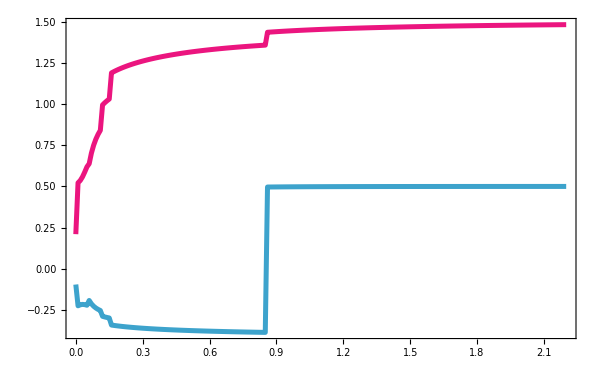

```mathematica
$FileName="Kitaev-S1.5_S0.5_ADA.m";

systemDimensions = {{2,2}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0 cvec}; 
bulkSpin         = {3/2};
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,2.2,.01};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 10; 
HamCoupling="XXZ_FM_ADA";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange; 

Print["h Range length= ",Length@hRange];


Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues,color1=cyan,color2=pink,
plotrange={{-.01,.78},{-.01,.78}}   },
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	
	{Lx,Ly}=Round@{Lx,Ly}; 
          scriptName= FileBaseName[$FileName]; 	
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataBulk=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];

(* Exporting to TXT*)
Module[{path1,path2},
path1=FileNameJoin@{Directory[],"data","ED_Kitaev","Spin",StringJoin[scriptName, "_Spin_Imp.txt"]};
path2=FileNameJoin@{Directory[],"data","ED_Kitaev","Spin",StringJoin[scriptName, "_Spin_Bulk.txt"]};
dataWrite[path1,dataSimp[[3]]  ]; 
dataWrite[path2,dataBulk[[3]]  ]; 
];

	plotTitle  = StringReplace[StringJoin[{"\\text{Adatom} \\quad  S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk "}],
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ JK  ],"g0"->ToString[Round@g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	

figSpinED=ListPlot[ {dataSimp[[3]], dataBulk[[3]]},PlotStyle->{{color1,Thickness[0.006] ,Opacity[1]},{color2,Thickness[0.006] ,Opacity[1]}},
Joined->True,
Frame->True,
FrameStyle->Directive[Black,18,Thickness[.002]],
PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)/@{"S_{\\text{imp} }","S_{1}"} },
LegendMarkers->Automatic],{Scaled[{.981,.9}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},
ImageSize->600,
PlotRange-> Full] 
]
```

## Figures - Substitution Case

### SUB S=1/2 Si=1/2 (Energy) (2x2)

h Range length= 201

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\Kitaev-S0.5_S0.5_SUB\XXZ_FM_SUB_size=(2,2)_Simp=0.5\h=Range[0,2,0.01]_JK={0.5}_k=20.txt

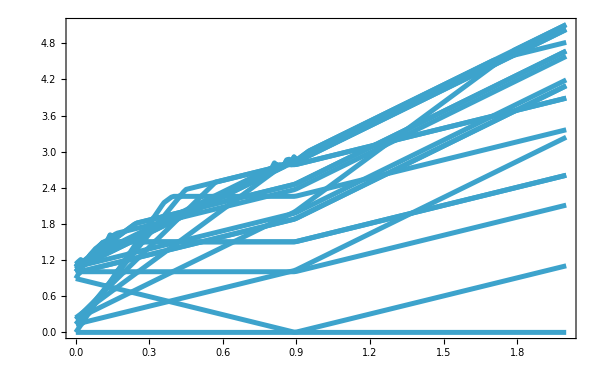

```mathematica
$FileName="Kitaev-S0.5_S0.5_SUB.m";

systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin         = {1/2};
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,2,.01};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 20; 
HamCoupling="XXZ_FM_SUB";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange; 

Print["h Range length= ",Length@hRange];


Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues,color1=cyan,color2=pink,
plotrange={{-.01,.78},{-.01,.78}}   },
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  Sort@dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	
(* Exporting to TXT*)
Module[{path0},
path0=FileNameJoin@{Directory[],"data","ED_Kitaev","Energy",StringJoin[scriptName, "_EN.txt"]};
dataWrite[path0,  Transpose[Thread/@levels]   ]; 
];


plotTitle  = StringReplace[StringJoin[{"\\text{Adatom} \\quad  S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk "}],
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ JK  ],"g0"->ToString[Round@g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	

figDispED0=ListPlot[Transpose[Thread/@levels],PlotStyle->{{color1,Thickness[0.006] ,Opacity[1]}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)@"\\text{ED}" },LegendMarkers->Automatic],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/K","\\omega/K"},ImageSize->600,
PlotRange-> Full] 
]
```

### SUB S=1/2 Si=1/2 (Spin) (2x2)

h Range length= 201

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\Kitaev-S0.5_S0.5_SUB\XXZ_FM_SUB_size=(2,2)_Simp=0.5\h=Range[0,2,0.01]_JK={0.5}_spin_components.txt

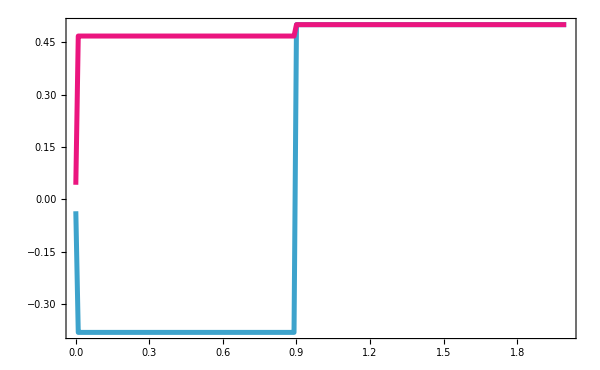

```mathematica
$FileName="Kitaev-S0.5_S0.5_SUB.m";

systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin         = {1/2};
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,2,.01};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 5; 
HamCoupling="XXZ_FM_SUB";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange; 

Print["h Range length= ",Length@hRange];



Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues,color1=cyan,color2=pink,
plotrange={{-.01,.78},{-.01,.78}}   },
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	
	{Lx,Ly}=Round@{Lx,Ly}; 
          scriptName= FileBaseName[$FileName]; 	
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataBulk=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];


	(* Exporting to TXT*)
Module[{path1,path2},
path1=FileNameJoin@{Directory[],"data","ED_Kitaev","Spin",StringJoin[scriptName, "_Spin_Imp.txt"]};
path2=FileNameJoin@{Directory[],"data","ED_Kitaev","Spin",StringJoin[scriptName, "_Spin_Bulk.txt"]};
dataWrite[path1,dataSimp[[3]]  ]; 
dataWrite[path2,dataBulk[[3]]  ]; 
];



plotTitle  = StringReplace[StringJoin[{"\\text{Substitution} \\quad  S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk "}],
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ JK  ],"g0"->ToString[Round@g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	

figSpinED=ListPlot[ {dataSimp[[3]], dataBulk[[3]]},PlotStyle->{{color1,Thickness[0.006] ,Opacity[1]},{color2,Thickness[0.006] ,Opacity[1]}},
Joined->True,
Frame->True,
FrameStyle->Directive[Black,18,Thickness[.002]],
PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)/@{"S_{\\text{imp} }","S_{1}"} },
LegendMarkers->Automatic],{Scaled[{.981,.9}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},
ImageSize->600,
PlotRange-> Full] 
]
```

### SUB S=3/2 Si=1/2 (Energy) (2x2)

h Range length= 441

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\Kitaev-S1.5_S0.5_SUB\XXZ_FM_SUB_size=(2,2)_Simp=0.5\h=Range[0,4.4,0.01]_JK={0.5}_k=20.txt

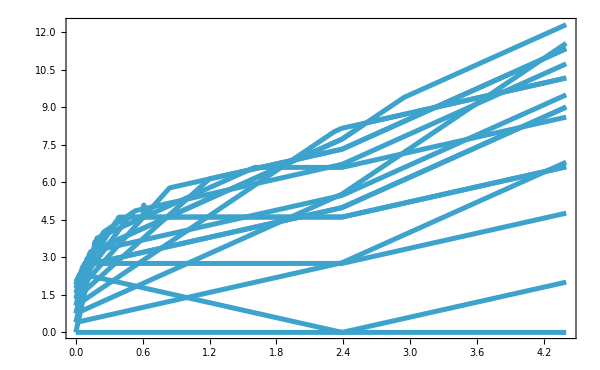

```mathematica
$FileName="Kitaev-S1.5_S0.5_SUB.m";

systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin         = {3/2};
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,4.4,.01};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 20; 
HamCoupling="XXZ_FM_SUB";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange; 

Print["h Range length= ",Length@hRange];


Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues,color1=cyan,color2=pink,
plotrange={{-.01,.78},{-.01,.78}},kmax=-1   },
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  Sort@dataRead[datapath];
kmax=-4;
	levels         = Transpose@{#[[;;,1]],(#[[;;,2,1;;kmax]]-#[[;;,2,1]])}&@eValues;
	
(* Exporting to TXT*)
Module[{path0},
path0=FileNameJoin@{Directory[],"data","ED_Kitaev","Energy",StringJoin[scriptName, "_EN.txt"]};
dataWrite[path0,  Transpose[Thread/@levels]   ]; 
];


plotTitle  = StringReplace[StringJoin[{"\\text{Substitution} \\quad  S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk "}],
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ JK  ],"g0"->ToString[Round@g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	

figDispED0=ListPlot[Transpose[Thread/@levels],PlotStyle->{{color1,Thickness[0.006] ,Opacity[1]}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)@"\\text{ED}" },LegendMarkers->Automatic],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/K","\\omega/K"},ImageSize->600,
PlotRange-> Full] 
]
```

### SUB S=3/2 Si=1/2 (Spin) (2x2)

h Range length= 221

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\Kitaev-S1.5_S0.5_SUB\XXZ_FM_SUB_size=(2,2)_Simp=0.5\h=Range[0,4.4,0.02]_JK={0.5}_spin_components.txt

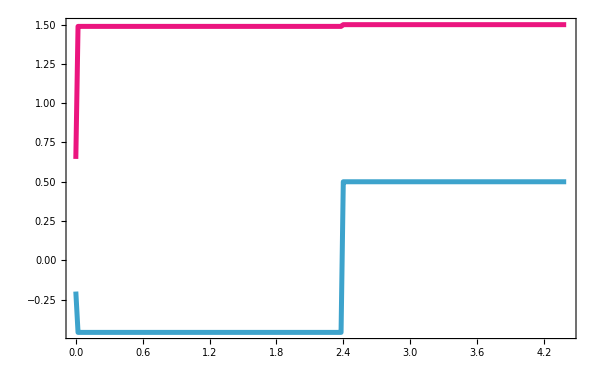

```mathematica
$FileName="Kitaev-S1.5_S0.5_SUB.m";

systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin         = {3/2};
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,4.4,.02};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 10; 
HamCoupling="XXZ_FM_SUB";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange; 

Print["h Range length= ",Length@hRange];



Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues,color1=cyan,color2=pink,
plotrange={{-.01,.78},{-.01,.78}}   },
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	
	{Lx,Ly}=Round@{Lx,Ly}; 
          scriptName= FileBaseName[$FileName]; 	
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataBulk=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];


	(* Exporting to TXT*)
Module[{path1,path2},
path1=FileNameJoin@{Directory[],"data","ED_Kitaev","Spin",StringJoin[scriptName, "_Spin_Imp.txt"]};
path2=FileNameJoin@{Directory[],"data","ED_Kitaev","Spin",StringJoin[scriptName, "_Spin_Bulk.txt"]};
dataWrite[path1,dataSimp[[3]]  ]; 
dataWrite[path2,dataBulk[[3]]  ]; 
];



plotTitle  = StringReplace[StringJoin[{"\\text{Substitution} \\quad  S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk "}],
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ JK  ],"g0"->ToString[Round@g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	

figSpinED=ListPlot[ {dataSimp[[3]], dataBulk[[3]]},PlotStyle->{{color1,Thickness[0.006] ,Opacity[1]},{color2,Thickness[0.006] ,Opacity[1]}},
Joined->True,
Frame->True,
FrameStyle->Directive[Black,18,Thickness[.002]],
PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)/@{"S_{\\text{imp} }","S_{1}"} },
LegendMarkers->Automatic],{Scaled[{.981,.9}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},
ImageSize->600,
PlotRange-> Full] 
]
```

### SUB S=1/2 Si=3/2 (Energy) (2x2)

h Range length= 101

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\Kitaev-S0.5_S1.5_SUB\XXZ_FM_SUB_size=(2,2)_Simp=1.5\h=Range[0,1,0.01]_JK={0.5}_k=6.txt

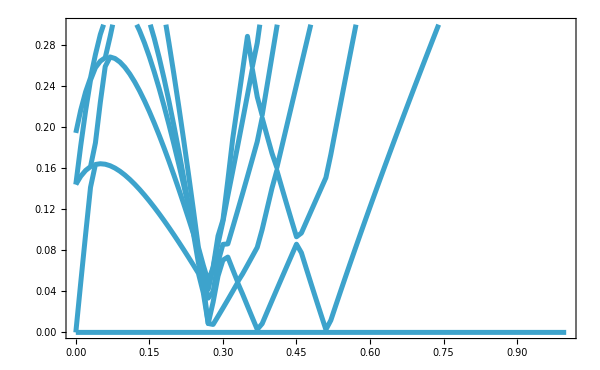

```mathematica
$FileName="Kitaev-S0.5_S1.5_SUB.m";

systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin         = {1/2};
impuritySpin     = {3/2};
gs               = {5};
KondoCoupling    = {.5};
hRange           = {0,1,.01};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 6; 
HamCoupling="XXZ_FM_SUB";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange; 

Print["h Range length= ",Length@hRange];


Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues,color1=cyan,color2=pink,
plotrange={{-.01,.78},{-.01,.78}}   },
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  Sort@dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	
(* Exporting to TXT*)
Module[{path0},
path0=FileNameJoin@{Directory[],"data","ED_Kitaev","Energy",StringJoin[scriptName, "_EN.txt"]};
dataWrite[path0,  Transpose[Thread/@levels]   ]; 
];


plotTitle  = StringReplace[StringJoin[{"\\text{Adatom} \\quad  S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk "}],
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ JK  ],"g0"->ToString[Round@g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	

figDispED0=ListPlot[Transpose[Thread/@levels],PlotStyle->{{color1,Thickness[0.006] ,Opacity[1]}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)@"\\text{ED}" },LegendMarkers->Automatic],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/K","\\omega/K"},ImageSize->600,
PlotRange-> {0,.3}] 
]
```

### SUB S=1/2 Si=3/2 (Spin) (2x2)

h Range length= 101

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\Kitaev-S0.5_S1.5_SUB\XXZ_FM_SUB_size=(2,2)_Simp=1.5\h=Range[0,1,0.01]_JK={0.5}_spin_components.txt

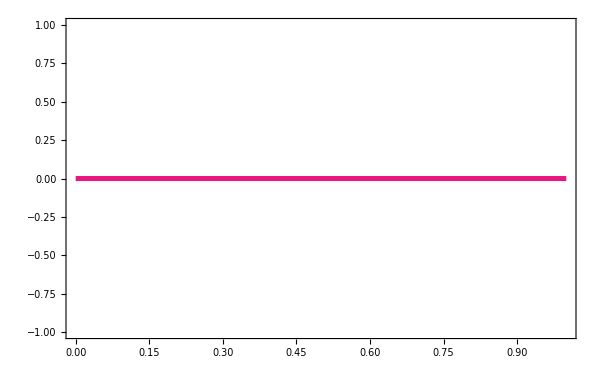

```mathematica
$FileName="Kitaev-S0.5_S1.5_SUB.m";

systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin         = {1/2};
impuritySpin     = {3/2};
gs               = {5};
KondoCoupling    = {.5};
hRange           = {0,1,.01};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 6; 
HamCoupling="XXZ_FM_SUB";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange; 

Print["h Range length= ",Length@hRange];



Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues,color1=cyan,color2=pink,
plotrange={{-.01,.78},{-.01,.78}}   },
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	
	{Lx,Ly}=Round@{Lx,Ly}; 
          scriptName= FileBaseName[$FileName]; 	
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataBulk=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];


	(* Exporting to TXT*)
Module[{path1,path2},
path1=FileNameJoin@{Directory[],"data","ED_Kitaev","Spin",StringJoin[scriptName, "_Spin_Imp.txt"]};
path2=FileNameJoin@{Directory[],"data","ED_Kitaev","Spin",StringJoin[scriptName, "_Spin_Bulk.txt"]};
dataWrite[path1,dataSimp[[3]]  ]; 
dataWrite[path2,dataBulk[[3]]  ]; 
];



plotTitle  = StringReplace[StringJoin[{"\\text{Substitution} \\quad  S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk "}],
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ JK  ],"g0"->ToString[Round@g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	

figSpinED=ListPlot[ {dataSimp[[3]], dataBulk[[3]]},PlotStyle->{{color1,Thickness[0.006] ,Opacity[1]},{color2,Thickness[0.006] ,Opacity[1]}},
Joined->True,
Frame->True,
FrameStyle->Directive[Black,18,Thickness[.002]],
PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)/@{"S_{\\text{imp} }","S_{1}"} },
LegendMarkers->Automatic],{Scaled[{.981,.9}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\left< \\mathbf{S}\\cdot\\hat{\\mathbf{c}} \\right> "},
ImageSize->600,
PlotRange-> Full] ;

ListPlot[ {dataSimp[[1]], dataBulk[[2]]},PlotStyle->{{color1,Thickness[0.006] ,Opacity[1]},{color2,Thickness[0.006] ,Opacity[1]}},
Joined->True,
Frame->True,
FrameStyle->Directive[Black,18,Thickness[.002]],
PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)/@{"S_{\\text{imp} }","S_{1}"} },
LegendMarkers->Automatic],{Scaled[{.981,.9}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\left< \\mathbf{S}\\cdot\\hat{\\mathbf{a}} \\right> "},
ImageSize->600,
PlotRange-> Full] 
]
```

### SUB S=1/2 Si=1 (Spin) (2x2)

```mathematica
parameters
```

{{{2.,2.},{0.,0.,0.},{-1.,-1.,-1.},{-0.057735,-0.057735,-0.057735},0.5,1.,5.,0.5}}

h Range length= 41

5.

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\Kitaev-S0.5_S1_SUB\XXZ_FM_SUB_size=(2,2)_Simp=1.0\h=Range[0,2,0.05]_JK={0.5}_spin_components.txt

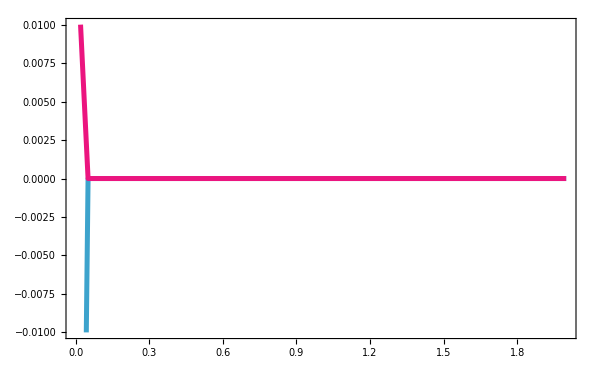

```mathematica
$FileName="Kitaev-S0.5_S1_SUB.m";

systemDimensions = {{2,2}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0.1 cvec}; 
bulkSpin         = {1/2};
impuritySpin     = {1};
gs               = {5};
KondoCoupling    = {.5};
hRange           = {0,2,.05};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 5; 
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange; 

Print["h Range length= ",Length@hRange];



Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues,color1=cyan,color2=pink,
plotrange={{-.01,.78},{-.01,.78}}   },
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	Print[g]; 
	{Lx,Ly}=Round@{Lx,Ly}; 
          scriptName= FileBaseName[$FileName]; 	
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath][[-Length@hRange;;-1]]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataBulk=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];


	(* Exporting to TXT*)
Module[{path1,path2},
path1=FileNameJoin@{Directory[],"data","ED_Kitaev","Spin",StringJoin[scriptName, "_Spin_Imp.txt"]};
path2=FileNameJoin@{Directory[],"data","ED_Kitaev","Spin",StringJoin[scriptName, "_Spin_Bulk.txt"]};
dataWrite[path1,dataSimp[[3]]  ]; 
dataWrite[path2,dataBulk[[3]]  ]; 
];



plotTitle  = StringReplace[StringJoin[{"\\text{Substitution} \\quad  S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk "}],
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ JK  ],"g0"->ToString[Round@g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	

figSpinED=ListPlot[ {dataSimp[[3]], dataBulk[[3]]},PlotStyle->{{color1,Thickness[0.006] ,Opacity[1]},{color2,Thickness[0.006] ,Opacity[1]}},
Joined->True,
Frame->True,
FrameStyle->Directive[Black,18,Thickness[.002]],
PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)/@{"S_{\\text{imp} }","S_{1}"} },
LegendMarkers->Automatic],{Scaled[{.981,.9}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\left< \\mathbf{S}\\cdot\\hat{\\mathbf{c}} \\right> "},
ImageSize->600,
PlotRange-> Full] ;

ListPlot[ {dataSimp[[2]], dataBulk[[2]]},PlotStyle->{{color1,Thickness[0.006] ,Opacity[1]},{color2,Thickness[0.006] ,Opacity[1]}},
Joined->True,
Frame->True,
FrameStyle->Directive[Black,18,Thickness[.002]],
PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)/@{"S_{\\text{imp} }","S_{1}"} },
LegendMarkers->Automatic],{Scaled[{.981,.9}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\left< \\mathbf{S}\\cdot\\hat{\\mathbf{a}} \\right> "},
ImageSize->600,
PlotRange-> {-0.01,0.01}] 
]
```

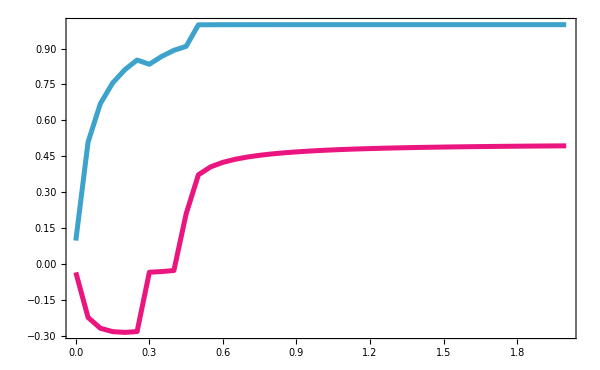

```mathematica
figSpinED
```